# Logistic Map - Base Function and related applications

The following notebook calculates some of the functions mentioned in the publication  ‘A Note on Exact Solutions of the Logistic Map, MF Maritz, to appear in Chaos (2020)’

The series solution, Section II B , Eq. (14), is calculated by BFUNC[λ,x].

The derivative of  BFUNC[λ,x] to x is calculated by DBFUNC[λ,x].

The numerical calculation of the base function, as discussed in Section II B, is performed with FFUNC[λ,x].

The numerical calculation of  the critical points ξ_0 and x_0 (as discussed in Section IV C and D) are calculated by XIZERO[λ] and XZERO[λ].

In order to activate all the functions, press the tab [Evaluation] , followed by [Evaluate Notebook].

# The Series Solution

BFUNC[λ,x] is the series solution up to order 20. For λ ∈ [2,4], it is recommended that the function be used only for x < 0.2. For larger values of x the accuracy may not be good.

```mathematica
x=.;  λ=.;
```

```mathematica
BFUNC[λ_,x_]:=x^2+x^4/(1-λ)+(2 x^6)/((-1+λ)^2 (1+λ))-(x^8 (5+λ))/((-1+λ)^3 (1+λ) (1+λ+λ^2))+(2 x^10 (7+3 λ+2 λ^2))/((-1+λ)^4 (1+λ)^2 (1+λ^2) (1+λ+λ^2))-(2 x^12 (21+14 λ+14 λ^2+8 λ^3+3 λ^4))/((-1+λ)^5 (1+λ)^2 (1+λ^2) (1+λ+λ^2) (1+λ+λ^2+λ^3+λ^4))+(4 x^14 (33+30 λ+37 λ^2+32 λ^3+27 λ^4+12 λ^5+8 λ^6+λ^7))/((-1+λ)^6 (1+λ)^3 (1+λ+λ^2)^2 (1+2 λ^2+λ^3+2 λ^4+λ^5+2 λ^6+λ^8))-(x^16 (429+495 λ+705 λ^2+756 λ^3+811 λ^4+660 λ^5+536 λ^6+327 λ^7+204 λ^8+89 λ^9+27 λ^10+λ^11))/((-1+λ)^7 (1+λ)^3 (1+λ^2) (1-λ+λ^2) (1+λ+λ^2)^2 (1+λ+λ^2+λ^3+λ^4) (1+λ+λ^2+λ^3+λ^4+λ^5+λ^6))+(2 x^18 (715+1001 λ+1595 λ^2+1980 λ^3+2435 λ^4+2494 λ^5+2570 λ^6+2159 λ^7+1854 λ^8+1359 λ^9+963 λ^10+537 λ^11+326 λ^12+126 λ^13+42 λ^14+4 λ^15))/((-1+λ)^8 (1+λ)^4 (1+λ^2)^2 (1-λ+λ^2) (1+λ+λ^2)^2 (1+λ^4) (1+λ+λ^2+λ^3+λ^4) (1+λ+λ^2+λ^3+λ^4+λ^5+λ^6))-(2 x^20 (2431+4004 λ+7007 λ^2+9735 λ^3+13200 λ^4+15510 λ^5+18128 λ^6+18703 λ^7+18794 λ^8+17392 λ^9+15554 λ^10+12643 λ^11+10138 λ^12+7226 λ^13+4894 λ^14+3059 λ^15+1743 λ^16+820 λ^17+353 λ^18+92 λ^19+14 λ^20))/((-1+λ)^9 (1+λ)^4 (1+λ^2)^2 (1-λ+λ^2) (1+λ+λ^2)^3 (1+λ^4) (1+λ+λ^2+λ^3+λ^4) (1+λ^3+λ^6) (1+λ+λ^2+λ^3+λ^4+λ^5+λ^6))
```

### Checking the cases λ=2 and λ=4

```mathematica
x=.
```

#### Checking the case λ=2

```mathematica
BFUNC[2,x]
```

x^2-x^4+(2 x^6)/3-x^8/3+(2 x^10)/15-(2 x^12)/45+(4 x^14)/315-x^16/315+(2 x^18)/2835-(2 x^20)/14175

```mathematica
Normal[Series[1/2*(1 - Exp[-2x^2]),{x,0,20}]]
```

x^2-x^4+(2 x^6)/3-x^8/3+(2 x^10)/15-(2 x^12)/45+(4 x^14)/315-x^16/315+(2 x^18)/2835-(2 x^20)/14175

#### Checking the case λ=4

```mathematica
BFUNC[4,x]
```

x^2-x^4/3+(2 x^6)/45-x^8/315+(2 x^10)/14175-(2 x^12)/467775+(4 x^14)/42567525-x^16/638512875+(2 x^18)/97692469875-(2 x^20)/9280784638125

```mathematica
Normal[Series[1/2*(1 - Cos[2x]),{x,0,20}]]
```

x^2-x^4/3+(2 x^6)/45-x^8/315+(2 x^10)/14175-(2 x^12)/467775+(4 x^14)/42567525-x^16/638512875+(2 x^18)/97692469875-(2 x^20)/9280784638125

### Series solution of the derivative of BFUNC

```mathematica
DBFUNC[la_,x_]:=D[BFUNC[la,t],t]/.t->x
```

### Checking one case

#### Checking the case λ=2

```mathematica
DBFUNC[2,x]
```

2 x-4 x^3+4 x^5-(8 x^7)/3+(4 x^9)/3-(8 x^11)/15+(8 x^13)/45-(16 x^15)/315+(4 x^17)/315-(8 x^19)/2835

```mathematica
Normal[Series[ 2 x Exp[-2x^2],{x,0,20}]]
```

2 x-4 x^3+4 x^5-(8 x^7)/3+(4 x^9)/3-(8 x^11)/15+(8 x^13)/45-(16 x^15)/315+(4 x^17)/315-(8 x^19)/2835

# The Base Function FFUNC (using iteration and the series solution)

The numerical calculation of the base function (as discussed in  Section II B) is performed with FFUNC[λ,x].

```mathematica
eps=10^(-12); la=.; x=.;
```

```mathematica
FFUNC[la_,x_]:={k=Ceiling[-2 Log[eps/x]/Log[la]],Xo=x*la^(-k/2),Yo=N[BFUNC[la,Xo],30],Nest[la * #*(1-#)&,Yo,k]}[[-1]]
```

### Plotting some cases

```mathematica
la=3;
```

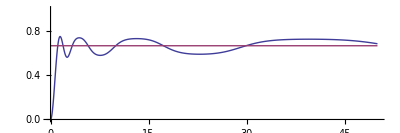

```mathematica
Plot[{FFUNC[la,x],(la-1)/la},{x,0,50},PlotRange->{0,1},AspectRatio->1/3]
```

```mathematica
la=N[1+Sqrt[5]];
```

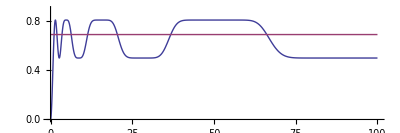

```mathematica
Plot[{FFUNC[la,x],(la-1)/la},{x,0,100},PlotRange->{0,0.9},AspectRatio->1/3]
```

```mathematica
la=3.5699456718;
```

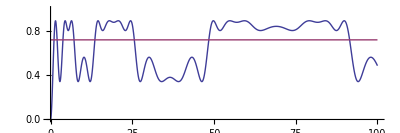

```mathematica
Plot[{FFUNC[la,x],(la-1)/la},{x,0,100},PlotRange->{0,1},AspectRatio->1/3]
```

```mathematica
la=4;
```

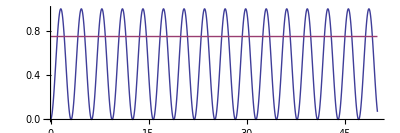

```mathematica
Plot[{FFUNC[la,x],(la-1)/la},{x,0,50},PlotRange->{0,1},AspectRatio->1/3]
```

### An animated display of FFUNC (shift the slider for changing λ)

```mathematica
Manipulate[Plot[FFUNC[LA,x],{x,0,40},PlotRange->{0,1}],{LA,2,4}]
```

### A 3D plot of FFUNC (Printing is suppressed here with the “;”, but should be removed to display the plot.)

```mathematica
Plot3D[FFUNC[la,x],{x,0,60},{la,2,4},PlotPoints->40,BoxRatios->{2,1,1/4},ColorFunction->"RedBlueTones",AxesLabel->{x,λ},LabelStyle->Directive[Large],TicksStyle->Small];
```

# Xi-zero and X-zero

The numerical calculation of  the critical points ξ_0 and x_0 (as discussed in Section IV D and depicted in Fig. 5) are calculated by XIZERO[λ] and XZERO[λ].

```mathematica
No=20;
```

```mathematica
XIZERO[la_]:={μ=(la-1)/la;, it=μ;, Do[it=N[(1 - Sqrt[1 - 4 it/la])/2,38],{k,1,No}],Y=it*la^No,XIo=Sqrt[Y]}[[-1]]
```

```mathematica
XZERO[la_]:={it=la/4; Do[it=N[(1 - Sqrt[1 - 4 it/la])/2,30],{k,1,No}],Y=it*la^No,Xo=Sqrt[Y]}[[-1]]
```

### Checking XIZERO[λ] and XZERO[λ] for λ=4

```mathematica
Grid[{{N[XIZERO[4]*3,15]},{ N[Pi,15]}}]
```

3.14159265358927
3.14159265358979

```mathematica
Grid[{{N[2*XZERO[4],15]},{N[Pi,15]}}]
```

3.14159265358862
3.14159265358979

### Plotting XIZERO[λ] and XZERO[λ] versus λ

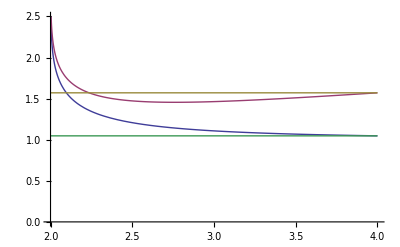

```mathematica
Plot[{XIZERO[la],XZERO[la],Pi/2,Pi/3},{la,2.0001,4},PlotRange->{0,2.5}]
```